Quantum Search Algorithm |

Householder Transformationpaclet:Q3/tutorial/QuantumSearchAlgorithm#1076935439 | Examplepaclet:Q3/tutorial/QuantumSearchAlgorithm#1481138763
Grover Rotationpaclet:Q3/tutorial/QuantumSearchAlgorithm#1497043023 | Notespaclet:Q3/tutorial/QuantumSearchAlgorithm#1668202417
Quantum Implementationpaclet:Q3/tutorial/QuantumSearchAlgorithm#1111568547 |

See also Section 4.5 of the Quantum Workbook (2022)https://doi.org/10.1007/978-3-030-91214-7.

The quantum search algorithm—also known as Grover’s algorithm after its inventor (Grover, 1996, 1997)—is a quantum algorithm to conduct an unstructured search. The unstructured search problem is to find a small number of elements with a specified property from within a huge unsorted (or, more generally, unstructured) data set. The quantum search algorithm finds a desired element with a high probability with an order of √N queries to the function that defines the property, where N is the size of the data set. Classical algorithms needs N queries.

Interestingly, the quantum search algorithm is known to be already optimal in the sense that any quantum algorithm for unstructured search needs an order of √N queries. In any case, the superiority of the quantum algorithm over its classical counterparts is merely quadratic (i.e., polynomial) rather than exponential. However, the quadratic speedup cannot be underestimated. The efficacy is considerable for large N.

Furthermore, the quantum search algorithm can apply to a wide range of problems. For example, it enables us to determine the existence and number of solutions of so-called NP-complete problems and to search exhaustively for the solutions.

Oraclepaclet:Q3/ref/OracleQ3 Package Symbol | Represents a quantum implementation of classical oracle.
Hadamardpaclet:Q3/ref/HadamardQ3 Package Symbol | The Hadamard gate on a single qubit.
CZpaclet:Q3/ref/CZQ3 Package Symbol | Controlled-Z gate.

Q3 functions used in the quantum search algorithm.

Make sure that the Q3 package is loaded to use the demonstrations in this document.

```mathematica
<<Q3`
```

Throughout this document, symbol S will be used to denote qubits and Pauli operators on them. Similarly, symbol c will be used to denote complex-valued coefficients.

```mathematica
Let[Qubit,S]
Let[Complex,c]
```

Householder Transformation

To understand and analyze the quantum search algorithm, it is convenient to introduce two closely related unitary operators. One is Householder transformation. Let v be a normalized vector in the Hilbert space. The Householder transformation associated with v is a unitary transformation defined by

U_v:=I-2vv.

Geometrically, it is a reflection in the hyperplane perpendicular to the vector v and containing the origin (null vector) as illustrated in Figure 1. For this reason, it is also known as Householder reflection.

-Graphics-

Figure 1. Geometric interpretation of the Householder transformation. Householder transformation U_v associated with a normalized vector v is a reflection in the hyperplane containing the origin and perpendicular to v.

The other is Grover’s diffusion operator. Grover’s diffusion operator associated with v is defined by

V_v:=2vv-I=-U_v.

It is a reflection in the line along the vector |v⟩ as shown in Figure 2. It can also be regarded as the Householder reflection U_v associated with the same vector v followed by another reflection through the origin as illustrated in the above figure.

-Graphics-

Figure 2. Geometric interpretation of Grover’s diffusion operator. Grover’s diffusion operator V_v with respect to v is a reflection in the line along the vector v. It can also be regarded as Householder transformation U_v associated with the same vector v followed by another reflection through the origin.

One can directly implement the Householder reflection U_v for a known state v. Suppose that v is achieved from 0≡0^(⊗n) by a unitary transformation W, v=W0. Then it follows that

U_v=W(1-200)W^†=W U_0 W^† .

Note that U_0 flips the phase of 0 to -0 but leaves other states unaffected. It is equivalent to writing

U_v:x_1,x_2,⋯,x_(n-1)⊗x_n↦x_1,x_2,⋯,x_(n-1)⊗(-Zx_n)

if x_1=x_1=⋯=x_1=0 and

U_v:x_1,x_2,⋯,x_(n-1)⊗x_n↦x_1,x_2,⋯,x_(n-1)⊗x_n

otherwise. It is a variant of multi-control Pauli-Z gate. More explicitly, U_0 for four qubits is described by the following quantum circuit

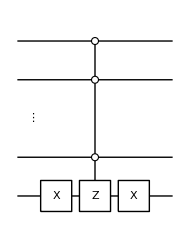
=-Graphics-

Overall, the Householder transformation U_v associated with v can be implemented by a quantum circuit of the form

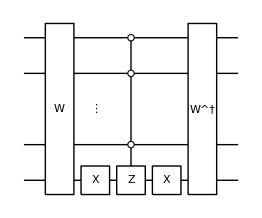

One can achieve Grover’s diffusion operator V_v for a known vector v in the same manner (up to a global phase factor −1).

Grover Rotation

```mathematica
<<Q3`
```

```mathematica
Let[Qubit,S]
Let[Complex,c]
```

Let us now describe the unstructured search problem more precisely. Suppose that we have a large list of items labeled by x = 0,1,2,… ,N−1. Among the items, there are a small number M (1 ≤ M ≪ N) of items with a unique property. The problem is to seek those items. The property is usually described by a classical oracle, f:{0,1}^n → {0,1}, where we assume N ≡ 2^n. The desired items are designated by the condition f(x)=1. In other words, an unstructured search is to find the solutions to the equation f(x)=1. This is why the quantum search algorithm applies to a broad class of problems where a function f(x) is well defined and can be evaluated without heavy cost.

We construct the quantum search algorithm combining Householder reflections and Grover’s diffusion operators. Let ℳ be the set of solutions,

ℳ={x:f(x)=1, x=0,1,2,…,2^n-1} .

Define a state of superposition consisting of the solutions

ω:=1/(√M)∑_(x∈ℳ) x ,

and another consisting of items that are not solutions

ω_⊥:=1/(√(N-M))∑_(x∉ℳ) x .

Obviously, they are orthogonal to each other, ωω_⊥=0. Neither of the two states are known and can be prepared. Rather, ω is the state we want to produce through the algorithm. Now consider the overall-superposition state, consisting all logical basis states

α:=1/(√N)∑_(x=0)^(N-1) x ,

which can be prepared by applying the Hadamard gates H^(⊗n) on 0. Since α involves both solutions and non-solutions, one can rewrite it into the form

α=ω √(M/N)+ω_⊥√((N-M)/N).

The advantage of the overall-superposition state α is that one can make use of the linearity of quantum mechanics—or quantum parallelism—to evaluate an operator on every state all at once. Indeed, applying the Householder reflection U_ω associated with the state vector ω on α produces

U_ω α=-ω √(M/N)+ω_⊥√((N-M)/N)=1/(√N)∑_(x=0)^(N-1) (x(-1))^(f(x)).

With a single operation of U_ω, we have flagged the states x associated with the solutions by the reversed phase factor −1. Unfortunately, however, we cannot directly single out those states. Instead, the tactic is to amplify the component along the state ω. This can be achieved by applying Grover’s diffusion operator V_α associated with α, U_ω α→V_α U_ω α. As illustrated geometrically in Figure 3 (left), it brings the state closer to the state ω.

-Graphics--Graphics-

Figure 3. Geometric interpretation of the quantum search algorithm. (left) The application of the Householder reflection U_ω followed by Grover’s diffusion operator V_α leads to the Grover rotation, G:=V_α U_ω, a rotation by angle 2θ, where θ is the angle between α and the horizontal axis. (right) Alternating applications of U_ω and V_α, or equivalently repeated applications of the Grover rotation G, bring α increasingly closer to ω.

At this stage, it is convenient to define the Grover rotation operator

G:=V_α U_ω .

G describes a rotation within the subspace spanned by ω and α towards the desired state ω. For a more quantitative analysis, we define the angle θ by

sin(θ/2)=√(M/N), cos(θ/2)=√((N-M)/N)

and

α=ωsin(θ/2)+ω_⊥cos(θ/2) .

It corresponds to the state rotated from ω_⊥ by angle θ around the axis perpendicular to both ω and ω_⊥ in the Bloch space corresponding to the two-dimensional subspace spanned by ω and ω_⊥. Accordingly, G corresponds to a rotation by angle 2θ around the same axis. This is illustrated in Figure 3 (right).

The k repeated applications of the Grover rotation G give

ψ_k=G^k α=ωsin((k+1/2)θ)+ω_⊥cos((k+1/2)θ) .

Starting from the overall-superposition state α, the resulting state ψ_k gets closest to the desired state ω when (k + 1/2)θ ≈ π/2. Therefore, the optimal number K of the Grover rotations to apply is given by

K=round(π/2θ-1/2) .

Assuming that M ≪ N, we observe that

θ≈2sin^-1(√(M/N))≈2 √(M/N)≪1 .

Then, it follows that

K≈π/4 √(N/M).

This means that we can find the solution by applying the Grover rotations G an order of √N times.

We can make the estimation of the performance more rigorous and get the
upper bound. Note that

θ/2≥sin(θ/2)=√(M/N),

where we have assumed that M≤N/2, and hence

K≤ceil(π/2θ)≤π/4 √(N/M).

Therefore, the above crude estimation turns out to be the worst case estimation.

Quantum Implementation

In the above, we have described the quantum search algorithm in terms of the Grover rotation consisting of the Householder reflection U_ω and Grover’s diffusion operator V_α. V_α can be implemented in terms of elementary gates because the state α is known. However, ω is unknown, and one cannot implement U_ω in a similar way.

Fortunately, we have noted above that the effect of U_ω is flagging the states x corresponding to the solutions with the reversed phase factor −1. One can achieve exactly the same effect by employing the quantum oracle  corresponding to the classical oracle f(x). In particular, with the ancillary qubit prepared in the state -:=(0-1)/√2, the quantum oracle induces a conditional phase shift as follows

x⊗-↦((x(-1))^(f(x)))⊗- .

In quantum circuit model, the identity is expressed as follows

-Graphics-

The overall quantum circuit to implement the Grover rotation is given in Figure 4 below.

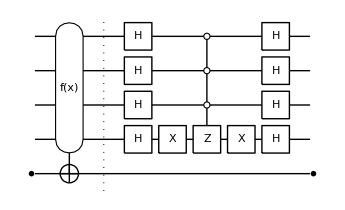

Figure 4. A quantum circuit for the Grover rotation. The first part before the vertical dashed line effectively implements the Householder transformation U_ω. The second part corresponds to Grover’s diffusion operator V_α.

Example

```mathematica
<<Q3`
```

Let us demonstrate the quantum search algorithm.

```mathematica
Let[Qubit,S,T]
Let[Complex,c]
```

We work with 4 (system) qubits and one ancillary qubit. The ancillary qubit is for the quantum oracle.

```mathematica
$n=4;
cc=Range[$n-1];
tt=$n;
kk=Range[$n];
```

Here, we specify a classical oracle in a more human readable way.

```mathematica
Clear[f]
f[3]=1;
f[_Integer]=0;
```

The ancilla qubit is prepared in the eigenstate of Pauli X operator belonging to eigenvalue -1.

```mathematica
in=ProductState[T->{1,-1}/Sqrt[2]];
in//Elaborate
```

(0_T)/(√2)-(1_T)/(√2)

Construct a quantum circuit for the Grover rotation.

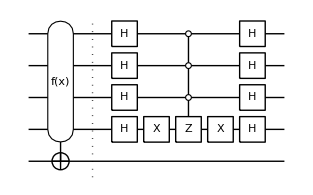

```mathematica
grv=QuantumCircuit[
Oracle[f,S[kk],T],"Separator",
S[kk,6],S[$n,1],ControlledGate[S[cc]->0,S[tt,3]],S[$n,1],S[kk,6],
"PortSize"->{0.5,0.2}
]
```

Apply the Grover rotation on the input state.

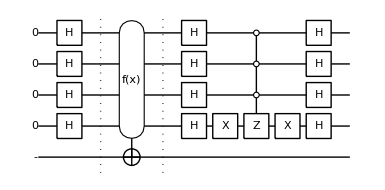

```mathematica
qc1=QuantumCircuit[Ket[S[kk]],{in,"Label"->"-"},S[kk,6],"Separator",grv]
```

Here is the resulting output state.

```mathematica
EchoTiming[out1=Elaborate[qc1]]
```

1.1859

-(3 0_S_10_S_20_S_30_S_40_T)/(16 √2)+(3 0_S_10_S_20_S_30_S_41_T)/(16 √2)-(3 0_S_10_S_20_S_31_S_40_T)/(16 √2)+(3 0_S_10_S_20_S_31_S_41_T)/(16 √2)-(3 0_S_10_S_21_S_30_S_40_T)/(16 √2)+(3 0_S_10_S_21_S_30_S_41_T)/(16 √2)-(11 0_S_10_S_21_S_31_S_40_T)/(16 √2)+(11 0_S_10_S_21_S_31_S_41_T)/(16 √2)-(3 0_S_11_S_20_S_30_S_40_T)/(16 √2)+(3 0_S_11_S_20_S_30_S_41_T)/(16 √2)-(3 0_S_11_S_20_S_31_S_40_T)/(16 √2)+(3 0_S_11_S_20_S_31_S_41_T)/(16 √2)-(3 0_S_11_S_21_S_30_S_40_T)/(16 √2)+(3 0_S_11_S_21_S_30_S_41_T)/(16 √2)-(3 0_S_11_S_21_S_31_S_40_T)/(16 √2)+(3 0_S_11_S_21_S_31_S_41_T)/(16 √2)-(3 1_S_10_S_20_S_30_S_40_T)/(16 √2)+(3 1_S_10_S_20_S_30_S_41_T)/(16 √2)-(3 1_S_10_S_20_S_31_S_40_T)/(16 √2)+(3 1_S_10_S_20_S_31_S_41_T)/(16 √2)-(3 1_S_10_S_21_S_30_S_40_T)/(16 √2)+(3 1_S_10_S_21_S_30_S_41_T)/(16 √2)-(3 1_S_10_S_21_S_31_S_40_T)/(16 √2)+(3 1_S_10_S_21_S_31_S_41_T)/(16 √2)-(3 1_S_11_S_20_S_30_S_40_T)/(16 √2)+(3 1_S_11_S_20_S_30_S_41_T)/(16 √2)-(3 1_S_11_S_20_S_31_S_40_T)/(16 √2)+(3 1_S_11_S_20_S_31_S_41_T)/(16 √2)-(3 1_S_11_S_21_S_30_S_40_T)/(16 √2)+(3 1_S_11_S_21_S_30_S_41_T)/(16 √2)-(3 1_S_11_S_21_S_31_S_40_T)/(16 √2)+(3 1_S_11_S_21_S_31_S_41_T)/(16 √2)

To analyze the result, we take the partial trace over the ancillary qubit. Note that the result is a density matrix.

```mathematica
new=Matrix@PartialTrace[out4,T];
```

The diagonal elements of the density matrix are the probability in the computational basis.

```mathematica
prb=Diagonal[new];
```

Observe how the amplitude corresponding to the desired item has been enhanced.

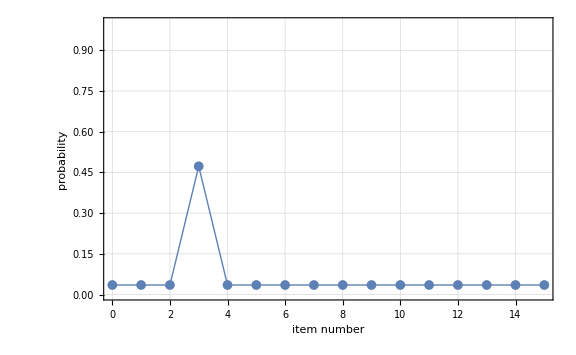

```mathematica
prb=Diagonal@Matrix[PartialTrace[out1,T],S@kk];
ListLinePlot[prb,DataRange->{0,Power[2,$n]-1},
PlotRange->{0,1},PlotMarkers->{Automatic,Medium},
FrameLabel->{"item number","probability"}]
```

Apply the Grover rotation again on the above output state.

```mathematica
qc2=QuantumCircuit[{out1,"Label"->"ψ"},grv]
```

-Graphics-

```mathematica
EchoTiming[out2=Elaborate[qc2];]
prb=Diagonal@Matrix[PartialTrace[out2,T],S@kk];
ListLinePlot[prb,DataRange->{0,Power[2,$n]-1},
PlotRange->{0,1},PlotMarkers->{Automatic,Medium},
FrameLabel->{"item number","probability"}]
```

1.15083

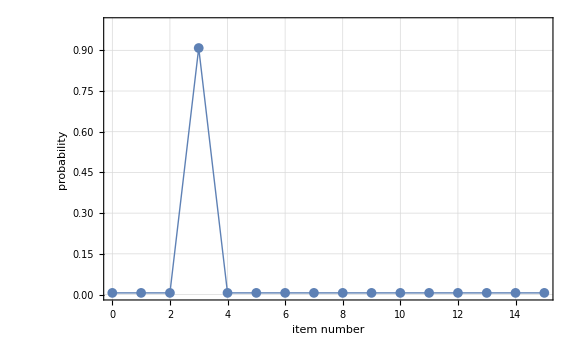

Repeat the same procedure.

```mathematica
qc3=QuantumCircuit[{out2,"Label"->"ψ"},grv]
```

-Graphics-

This must be optimal and is the final state.

```mathematica
EchoTiming[out3=Elaborate[qc3];]
prb=Diagonal@Matrix[PartialTrace[out3,T],S@kk];
ListLinePlot[prb,DataRange->{0,Power[2,$n]-1},
PlotRange->{0,1},PlotMarkers->{Automatic,Medium},
FrameLabel->{"item number","probability"}]
```

1.1562

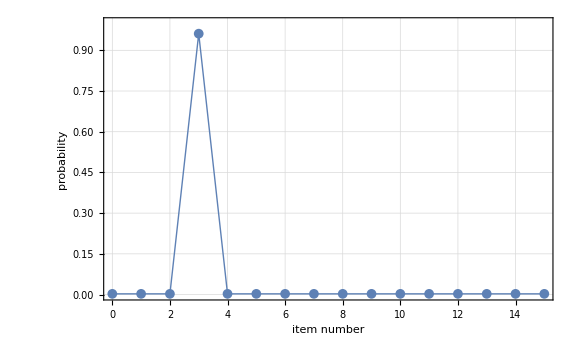

Any further application of the Grover rotation will overshoot the desired result.

```mathematica
qc4=QuantumCircuit[{out3,"Label"->"ψ"},grv]
```

-Graphics-

Observe that the output state overshoot.

```mathematica
EchoTiming[out4=Elaborate[qc4];]
prb=Diagonal@Matrix[PartialTrace[out4,T],S@kk];
ListLinePlot[prb,DataRange->{0,Power[2,$n]-1},
PlotRange->{0,1},PlotMarkers->{Automatic,Medium},
FrameLabel->{"item number","probability"}]
```

1.15307

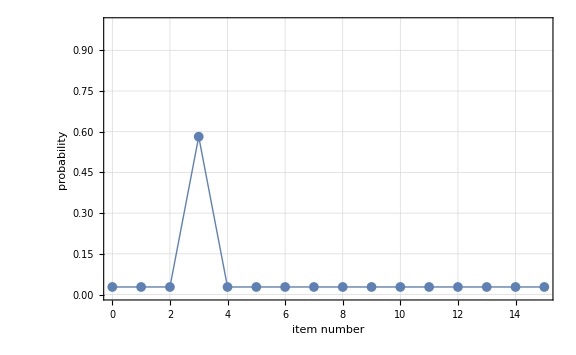

Notes

The process explained here can also be regarded as (or generalized to) quantum amplitude amplification; see Brassard et al. (2002).

It has been assumed that the number M of solutions is known. It is also possible to achieve similar speed-up even if M is not known. See Brassard et al. (2002).

| Related Guides
▪Quantum Information Systems

| Related Tech Notes
▪Quantum Algorithms
▪Quantum Information Systems with Q3

| Related Links
▪L. K. Grover (1996)http://arxiv.org/abs/quant-ph/9605043, “A fast quantum mechanical algorithm for database search,” in Proceedings of the 28th Annual ACM Symposium on the Theory of Computing (ACM Press, New York, 1996), p. 212.
▪L. K. Grover, Physical Review Letters 79, 325 (1997)https://doi.org/10.1103/PhysRevLett.79.325, "Quantum Mechanics Helps in Searching for a Needle in a Haystack."
▪G. Brassard, P. Høyer, M. Mosca, A. Tapp, Contemporary Mathematics 305, 53 (2002)https://doi.org/10.1090/conm/305/05215, "Quantum amplitude amplification and estimation".
▪T. J. Yoder, G. H. Low and I. L. Chuang, Physical Review Letters 113, 210501 (2014)https://doi.org/10.1103/physrevlett.113.210501, "Fixed-Point Quantum Search with an Optimal Number of Queries".
▪M. Nielsen and I. L. Chuang (2022)https://doi.org/10.1017/CBO9780511976667, Quantum Computation and Quantum Information (Cambridge University Press).
▪Mahn-Soo Choi (2022)https://doi.org/10.1007/978-3-030-91214-7, A Quantum Computation Workbook (Springer).